# Calculate and write higher order moments

Params

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=1000;
```

```mathematica
nTime=200;
```

```mathematica
dt=0.01;
```

Functions

```mathematica
latt=Import["../data/ic_v"<>IntegerString[1,10,3]<>"/lattice_v"<>IntegerString[1,10,3]<>"/lattice/"<>IntegerString[0,10,4]<>".txt","Table"][[;;,1]];
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
count3=Length[Select[Range[1,Length[l1]],l1[[#]]==1&&l2[[#]]==1&]]
```

0

```mathematica
l1=latt[[2;;-2]]-latt[[;;-3]];
```

Part::take: Cannot take positions 2 through -2 in Symbol[].

Part::take: Cannot take positions 1 through -3 in Symbol[].

```mathematica
l2=latt[[3;;]]-latt[[2;;-2]];
```

Part::take: Cannot take positions 3 through -1 in Symbol[].

Part::take: Cannot take positions 2 through -2 in Symbol[].

```mathematica
tripletCount
```

tripletCount

```mathematica
count[ic_,lattIdx_]:=Module[
{latt,lattComplete,tripletCount,tripletCounts,quarticCount,quarticCounts,l1,l2,l3,l4,l5},

tripletCounts={};
quarticCounts={};
Do[

latt=Import["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt","Table"][[;;,1]];

l1=latt[[2;;-2]]-latt[[;;-3]];
l2=latt[[3;;]]-latt[[2;;-2]];
tripletCount=Length[Select[Range[1,Length[l1]],l1[[#]]==1&&l2[[#]]==1&]];

l3=latt[[2;;-3]]-latt[[;;-4]];
l4=latt[[3;;-2]]-latt[[2;;-3]];
l5=latt[[4;;]]-latt[[3;;-2]];
quarticCount=Length[Select[Range[1,Length[l3]],l3[[#]]==1&&l4[[#]]==1&&l5[[#]]==1&]];

AppendTo[tripletCounts,tripletCount];
AppendTo[quarticCounts,quarticCount];
,{t,0,nTime}];

Return[{tripletCounts,quarticCounts}];
];
```

```mathematica
countOLD[ic_,lattIdx_]:=Module[
{latt,lattComplete,tripletCount,tripletCounts,quarticCount,quarticCounts},

tripletCounts={};
quarticCounts={};
Do[

latt=Import["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt","Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
Do[
lattComplete[[l]]=1;
,{l,latt}];

tripletCount=0;
quarticCount=0;
Do[
If[lattComplete[[i]]==1&&lattComplete[[i+1]]==1&&lattComplete[[i+2]]==1,
tripletCount+=1;
If[i!=Length[lattComplete]-2&&lattComplete[[i+3]]==1,
quarticCount+=1;
];
];
,{i,1,Length[lattComplete]-2}];

AppendTo[tripletCounts,tripletCount];
AppendTo[quarticCounts,quarticCount];
,{t,0,nTime}];

Return[{tripletCounts,quarticCounts}];
];
```

```mathematica
count[ic_,lattIdx_]:=Module[
{latt,lattComplete,tripletCount,tripletCounts,quarticCount,quarticCounts},

tripletCounts={};
quarticCounts={};
Do[

latt=Import["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt","Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
Do[
lattComplete[[l]]=1;
,{l,latt}];

tripletCount=0;
quarticCount=0;
Do[
If[lattComplete[[i]]==1&&lattComplete[[i+1]]==1&&lattComplete[[i+2]]==1,
tripletCount+=1;
If[i!=Length[lattComplete]-2&&lattComplete[[i+3]]==1,
quarticCount+=1;
];
];
,{i,1,Length[lattComplete]-2}];

AppendTo[tripletCounts,tripletCount];
AppendTo[quarticCounts,quarticCount];
,{t,0,nTime}];

Return[{tripletCounts,quarticCounts}];
];
```

```mathematica
fWriteTriplets[ic_,lattIdx_,triplets_]:=Module[
{f}
,
CreateDirectory["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/triplets"];
f=OpenWrite["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/triplets/A_A_A.txt"];
Do[
WriteString[f,ToString[(i-1)*dt]<>" "<>ToString[triplets[[i]]]<>"\n"];
,{i,1,Length[triplets]}];
Close[f];
];
```

```mathematica
fWriteQuartics[ic_,lattIdx_,quartics_]:=Module[
{f}
,
CreateDirectory["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/quartics"];
f=OpenWrite["../data/ic_v"<>IntegerString[ic,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/quartics/A_A_A_A.txt"];
Do[
WriteString[f,ToString[(i-1)*dt]<>" "<>ToString[quartics[[i]]]<>"\n"];
,{i,1,Length[quartics]}];
Close[f];
];
```

Calculate and write moments

```mathematica
icIdxStart=1;
icIdxEnd=50;
```

```mathematica
lattIdxStart=1;
lattIdxEnd=50;
```

```mathematica
Monitor[
Do[
Do[
{triplets,quartics}=count[icIdx,lattIdx];
Quiet[fWriteTriplets[icIdx,lattIdx,triplets]];
Quiet[fWriteQuartics[icIdx,lattIdx,quartics]];
,{lattIdx,lattIdxStart,lattIdxEnd}];
,{icIdx,icIdxStart,icIdxEnd}];
,Column[{
ProgressIndicator[lattIdx,{lattIdxStart,lattIdxEnd}],
ProgressIndicator[icIdx,{icIdxStart,icIdxEnd}]
}]]
```

# Check moments

```mathematica
icIdx=2;
```

```mathematica
lattIdxStart=1;
lattIdxEnd=100;
```

```mathematica
SetDirectory[NotebookDirectory[]];
m1={};
m2={};
m3={};
m4={};
Do[
AppendTo[m1,Import["../data/ic_v"<>IntegerString[icIdx,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/counts/A.txt","Table"][[1,2]]];
AppendTo[m2,Import["../data/ic_v"<>IntegerString[icIdx,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/nns/A_A.txt","Table"][[1,2]]];
AppendTo[m3,Import["../data/ic_v"<>IntegerString[icIdx,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/triplets/A_A_A.txt","Table"][[1,2]]];
AppendTo[m4,Import["../data/ic_v"<>IntegerString[icIdx,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/quartics/A_A_A_A.txt","Table"][[1,2]]];
,{lattIdx,lattIdxStart,lattIdxEnd}];
```

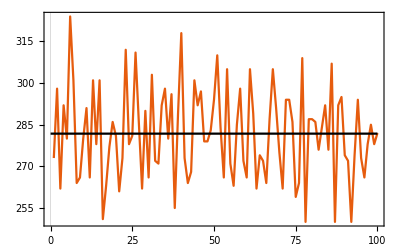

```mathematica
Show[ListLinePlot[m1],Plot[Mean[m1],{x,0,100},PlotStyle->Black]]
```

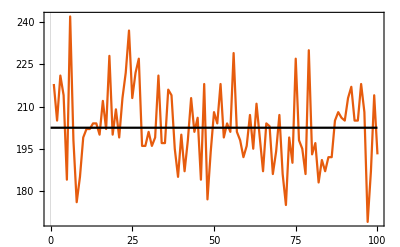

```mathematica
Show[ListLinePlot[m2],Plot[Mean[m2],{x,0,100},PlotStyle->Black]]
```

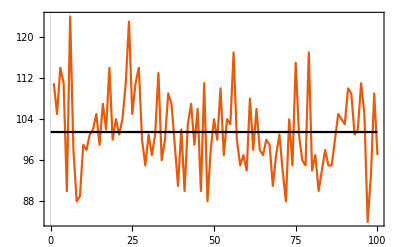

```mathematica
Show[ListLinePlot[m3],Plot[Mean[m3],{x,0,100},PlotStyle->Black]]
```

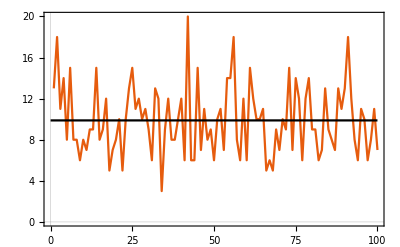

```mathematica
Show[ListLinePlot[m4],Plot[Mean[m4],{x,0,100},PlotStyle->Black]]
```

```mathematica
Mean[m1]//N
```

402.33

```mathematica
Mean[m2]//N
```

202.46

```mathematica
Mean[m3]//N
```

101.5

```mathematica
Mean[m4]//N
```

9.88